```mathematica
ker[ee_NumericQ,pp_NumericQ,ϵ_NumericQ]:=pp^2/(ee-pp^2+I ϵ)
```

```mathematica
NIntegrate[Re[ker[energie,mom,eps]],{mom,0,100}]
```

-98.4392

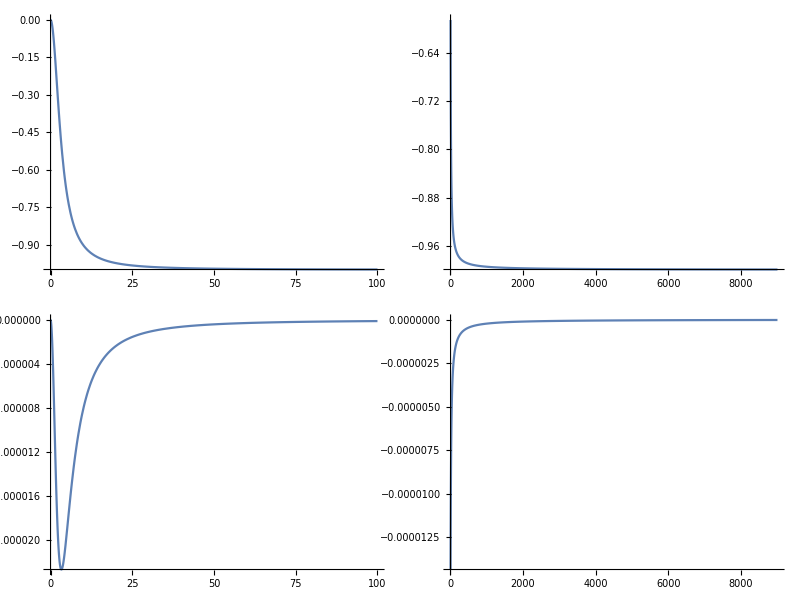

```mathematica
energie=-11;eps=0.001;pmax=9000;cfe=1.;
Grid[{{Plot[Re[ker[energie,mom,eps]],{mom,0,100},PlotRange->Full],
Plot[NIntegrate[Re[Λ^-cfe ker[energie,mom,eps]],{mom,0,Λ}],{Λ,10,pmax},PlotRange->Full]},{Plot[Im[ker[energie,mom,eps]],{mom,0,100},PlotRange->Full],
Plot[NIntegrate[Im[Λ^-cfe ker[energie,mom,eps]],{mom,0,Λ}],{Λ,10,pmax},PlotRange->Full]}}]
```

```mathematica
kert[ee_,pp_NumericQ,ss_,eps_]:=pp^2 Exp[I ss (pp^2-ee+I eps)]
```

```mathematica
kert[e,p,s,ep]/.{e->1,p->2,s->3,ep->0.1}
```

-2.69993+1.22122 ⅈ

```mathematica
energie=10;eps=0.01;pmax=9000;ss=0.1;
NIntegrate[Re[kert[energie,mom,ss,eps]],{mom,0,10}]
```

21.3565

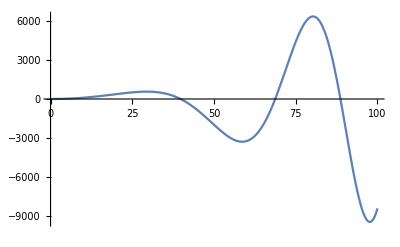

```mathematica
energie=10.1;pmax=100;cfe=0;ss=0.001;
Plot[Re[kert[energie,mom,ss,eps]],{mom,0,pmax},PlotRange->Full]
(*Grid[{{Plot[Re[kert[energie,mom,ss]],{mom,0,100},PlotRange->Full],
Plot[NIntegrate[Re[Λ^-cfe kert[energie,mom,ss]],{mom,0,Λ}],{Λ,10,pmax},PlotRange->Full]},{Plot[Im[kert[energie,mom,ss]],{mom,0,100},PlotRange->Full],
Plot[NIntegrate[Im[Λ^-cfe kert[energie,mom,ss]],{mom,0,Λ}],{Λ,10,pmax},PlotRange->Full]}}]*)
```